```mathematica
R1=400;C1=4;L1=16;
```

```mathematica
R2=1;L2=1;C2=1;
```

```mathematica
R3=25;C3=4;L3=16;
```

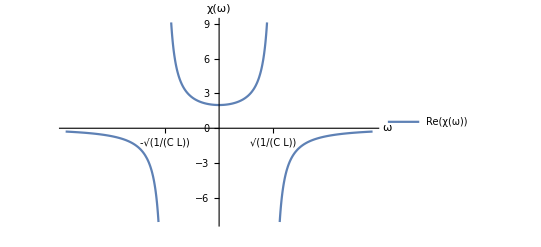

```mathematica
Plot[{1/(-ω^2+1/2)}, {ω,-2,2},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{{{1/Sqrt[2],Sqrt[1/(L C)]},{-1/Sqrt[2],-Sqrt[1/(L C)]}},{None}}]
```

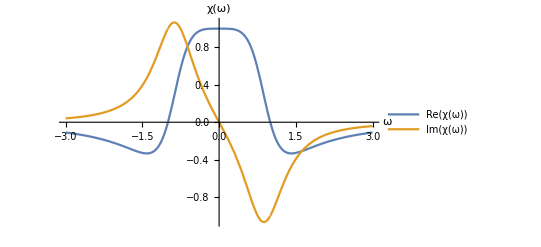

```mathematica
Plot[{Re[1/(ⅈ ω-ω^2+1)],Im[1/(ⅈ ω-ω^2+1)]}, {ω,-3,3},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

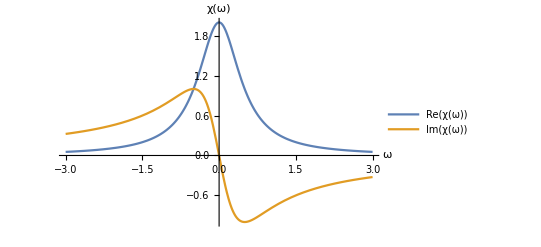

```mathematica
Plot[{Re[1/(ⅈ ω+1/2)],Im[1/(ⅈ ω+1/2)]}, {ω,-3,3},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

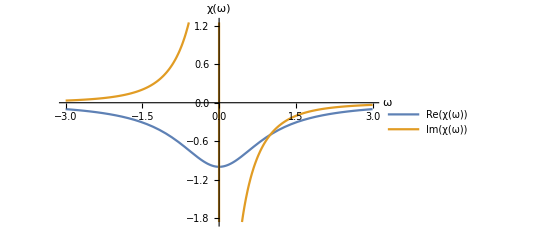

```mathematica
Plot[{Re[1/(ⅈ ω-ω^2)],Im[1/(ⅈ ω-ω^2)]}, {ω,-3,3},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

```mathematica
ωp=1/10; τ=100;
```

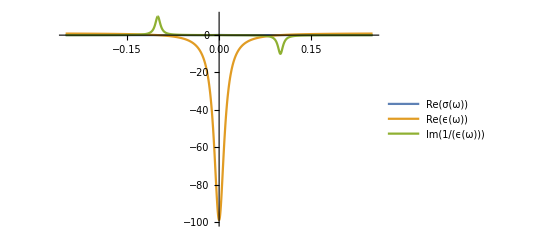

```mathematica
Plot[{ωp^2/(4Pi τ)1/(1/τ^2+ω^2),1-ωp^2/(1/τ^2+ω^2),-ω/τ ωp^2/((ω^2-ωp^2)^2+ω^2/τ^2)},{ω,-0.25,0.25},PlotLegends->{Re[σ[ω]],Re[ϵ[ω]],Im[1/ϵ[ω]]},PlotRange->{-100,10},Ticks->{None}]
```

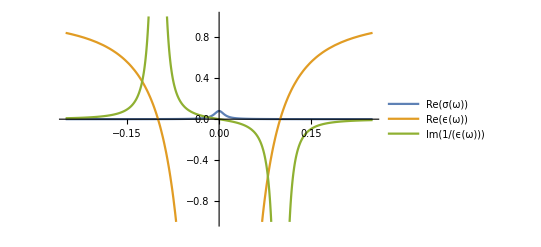

```mathematica
Plot[{ωp^2/(4Pi τ)1/(1/τ^2+ω^2),1-ωp^2/(1/τ^2+ω^2),-ω/τ ωp^2/((ω^2-ωp^2)^2+ω^2/τ^2)},{ω,-0.25,0.25},PlotLegends->{Re[σ[ω]],Re[ϵ[ω]],Im[1/ϵ[ω]]},PlotRange->{-1,1},Ticks->{None}]
```

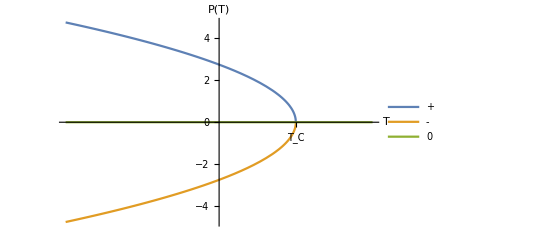

```mathematica
Plot[{Sqrt[3/2(5-t)],-Sqrt[3/2(5-t)],0},{t,-10,10},PlotLegends->{"+","-",0},Ticks->{{{5,Subscript[T, C]}},{None}},AxesLabel->{T,P[T],0}]
```

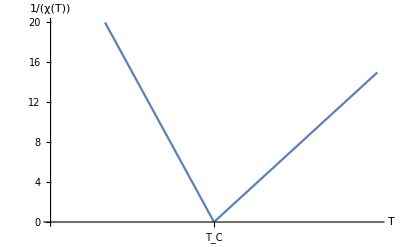

```mathematica
Plot[{6(5-t),3(t-5)},{t,0,10},Ticks->{{{5,Subscript[T, C]}},{None}},AxesLabel->{T,1/χ[T]},PlotRange->{0,20},PlotStyle->ColorData[97,1]]
```

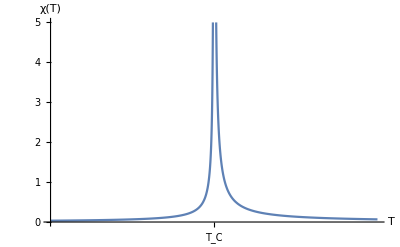

```mathematica
Plot[{1/(6(5-t)),1/(3(t-5))},{t,0,10},Ticks->{{{5,Subscript[T, C]}},{None}},AxesLabel->{T,χ[T]},PlotRange->{0,5},PlotStyle->ColorData[97,1]]
```

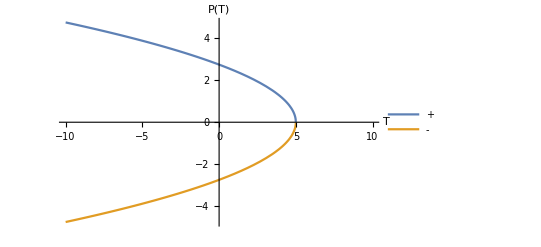

```mathematica
Plot[{√((3 (5-t))/2),-√((3 (5-t))/2)},{t,-10,10},PlotLegends->{"+","-"},
Ticks->{None},AxesLabel->{T,P[T]}]
```

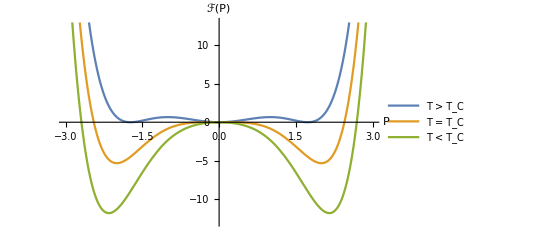

```mathematica
Plot[{3/2 p^2-p^4+1/6 p^6,-p^4+1/6 p^6,-3/2 p^2-p^4+1/6 p^6},{p,-3,3},PlotRange->{-13,13},PlotLegends->{"T > T_C","T = T_C","T < T_C"},AxesLabel->{P,ℱ[P]},Ticks->{None}]
```

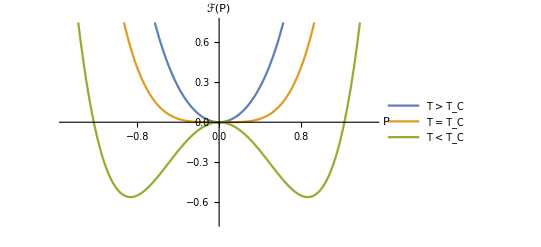

```mathematica
Plot[{3/2 p^2+p^4,p^4,-3/2 p^2+p^4},{p,-1.5,1.5},PlotRange->{-0.75,0.75},PlotLegends->{"T > T_C","T = T_C","T < T_C"},AxesLabel->{P,ℱ[P]},Ticks->{None}]
```

```mathematica
ϵω[ωp_,ω_,τ_]:=1-ωp^2/(ω^2+ⅈ ω/τ)
```

```mathematica
Nω[ωp_,ω_,τ_]:=Sqrt[ϵω[ωp,ω,τ]]
```

```mathematica
Ref[ωp_,ω_,τ_]:=Abs[(1-Nω[ωp,ω,τ])/(1+Nω[ωp,ω,τ])]^2
```

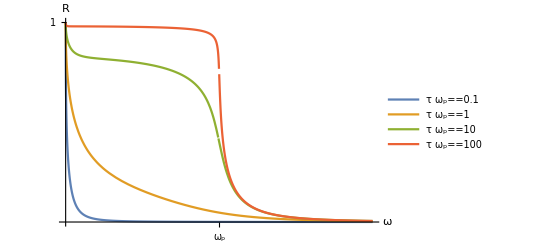

```mathematica
Plot[{Ref[1,ω,0.1],Ref[1,ω,1],Ref[1,ω,10],Ref[1,ω,100]},{ω,0,2},Ticks->{{{1,Subscript[ω, p]}},{{1,1}}},AxesLabel->{ω,R},PlotLegends->{τ Subscript[ω, p]==0.1,τ Subscript[ω, p]==1,τ Subscript[ω, p]==10,τ Subscript[ω, p]==100}]
```

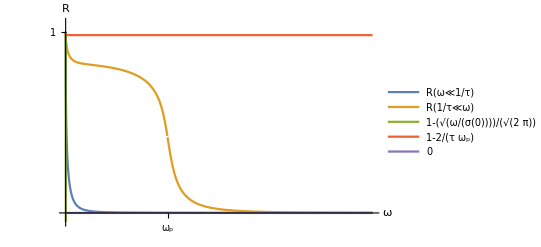

```mathematica
Plot[{Ref[1,ω,0.1],Ref[1,ω,10],1-2Sqrt[(2ω)/0.01],1-2/100,0},{ω,0,3},PlotRange->{-0.05,1.05},Ticks->{{{1,Subscript[ω, p]}},{{1,1}}},AxesLabel->{ω,R},PlotLegends->{R[ω≪1/τ],R[1/τ≪ω],1-Sqrt[ω/(2Pi σ[0])],1-2/(Subscript[ω, p] τ),0}]
```

```mathematica
Series[1/(x+1),{x,0,1}]
```

1-x+O[x]^2

```mathematica
Series[(N-1)/(1+N),{N,Infinity,1}]
```

1-2/N+O[1/N]^2

```mathematica
Series[Sqrt[1-x],{x,0,1}]
```

1-x/2+O[x]^2

```mathematica
Series[1/(ⅈ ω)
```